## Laplace’s equation on a disk

```mathematica
Subscript[vc, m_][ϕ_]=Cos[m ϕ]
```

cos(m ϕ)

```mathematica
Subscript[vs, m_][ϕ_]=Sin[m ϕ]
```

sin(m ϕ)

```mathematica
a=1
```

1

```mathematica
IP[u_,v_]:=Integrate[u v,{ϕ,-Pi,Pi}]
```

```mathematica
Subscript[Ac, m_]:= 1/a^m IP[Subscript[vc, m][ϕ],Subscript[U, 0][ϕ]]/IP[Subscript[vc, m][ϕ],Subscript[vc, m][ϕ]]
```

```mathematica
Subscript[As, m_]:= 1/a^m IP[Subscript[vs, m][ϕ],Subscript[U, 0][ϕ]]/IP[Subscript[vs, m][ϕ],Subscript[vs, m][ϕ]]
```

```mathematica
uSum[M_,ρ_,ϕ_]:=Subscript[Ac, 0]+Sum[
Subscript[Ac, m] ρ^m Subscript[vc, m][ϕ]+ Subscript[As, m] ρ^m Subscript[vs, m][ϕ],
{m,1,M}]
```

## Example 1

```mathematica
Subscript[U, 0][ϕ_]=Cos[2ϕ]+1/4Sin[3ϕ]
```

1/4 sin(3 ϕ)+cos(2 ϕ)

```mathematica
u8[ρ_,ϕ_]=uSum[8,ρ,ϕ]
```

1/4 ρ^3 sin(3 ϕ)+ρ^2 cos(2 ϕ)

```mathematica
RevolutionPlot3D[u8[ρ,ϕ],{ρ,0,a},{ϕ,-π,π},PlotRange->All,PlotTheme->"ZMesh",PlotPoints->128]
```

-Graphics3D-

## Example 2

```mathematica
Subscript[U, 0][ϕ_]=Piecewise[{{Cos[2ϕ],Abs[ϕ]<Pi/4}}]
```

Piecewise[{{cos(2 ϕ), Abs[ϕ]<π/4}, {0, True}}]

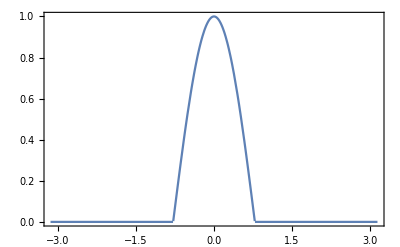

```mathematica
Plot[Subscript[U, 0][ϕ],{ϕ,-Pi,Pi}]
```

```mathematica
u32[ρ_,ϕ_]=uSum[32,ρ,ϕ]
```

-(ρ^32 cos(32 ϕ))/(255 π)-(2 √2 ρ^31 cos(31 ϕ))/(957 π)+(2 √2 ρ^29 cos(29 ϕ))/(837 π)+(ρ^28 cos(28 ϕ))/(195 π)+(2 √2 ρ^27 cos(27 ϕ))/(725 π)-(2 √2 ρ^25 cos(25 ϕ))/(621 π)-(ρ^24 cos(24 ϕ))/(143 π)-(2 √2 ρ^23 cos(23 ϕ))/(525 π)+(2 √2 ρ^21 cos(21 ϕ))/(437 π)+(ρ^20 cos(20 ϕ))/(99 π)+(2 √2 ρ^19 cos(19 ϕ))/(357 π)-(2 √2 ρ^17 cos(17 ϕ))/(285 π)-(ρ^16 cos(16 ϕ))/(63 π)-(2 √2 ρ^15 cos(15 ϕ))/(221 π)+(2 √2 ρ^13 cos(13 ϕ))/(165 π)+(ρ^12 cos(12 ϕ))/(35 π)+(2 √2 ρ^11 cos(11 ϕ))/(117 π)-(2 √2 ρ^9 cos(9 ϕ))/(77 π)-(ρ^8 cos(8 ϕ))/(15 π)-(2 √2 ρ^7 cos(7 ϕ))/(45 π)+(2 √2 ρ^5 cos(5 ϕ))/(21 π)+(ρ^4 cos(4 ϕ))/(3 π)+(2 √2 ρ^3 cos(3 ϕ))/(5 π)+1/4 ρ^2 cos(2 ϕ)+(2 √2 ρ cos(ϕ))/(3 π)+1/(2 π)

```mathematica
RevolutionPlot3D[u32[ρ,ϕ],{ρ,0,a},{ϕ,0,2π},PlotRange->All,PlotTheme->"ZMesh",PlotPoints->128]
```

-Graphics3D-